# Supplement to TASI Lecture 2 of “QIS for Particle Theorists”

THIS NOTEBOOK CREATED BY J. LYKKEN

## Some basic operations and definitions

```mathematica
Id[N_]=IdentityMatrix[N]; (* NxN identity matrix *)
ZeroM[N_]:=ConstantArray[0,{N,N}]; (* NxN matrix of zeroes *)
KP[a_,b_]:=KroneckerProduct[a,b]; (* the Kronecker tensor product *)

(* some basic single and two qubit unitary operations as a reminder *)
x=({{0, 1}, {1, 0}});
y=({{0, -I}, {I, 0}});
z=({{1, 0}, {0, -1}});
sp=({{0, 1}, {0, 0}});
sm=({{0, 0}, {1, 0}});
P0 = ({{1, 0}, {0, 0}});
P1 = ({{0, 0}, {0, 1}});
hadamard=1/(√2)({{1, 1}, {1, -1}});
(* Define a Hadamard gate on the kth qubit of nqubits: *)
Hadamard[k_,nqubits_]:=KP[Id[2^(k-1)],KP[hadamard,Id[2^(nqubits-k)]]];

(* Define other single qubit operations on the kth qubit of nqubits: *)
X[k_,nqubits_]:=KP[Id[2^(k-1)],KP[x,Id[2^(nqubits-k)]]];
Y[k_,nqubits_]:=KP[Id[2^(k-1)],KP[y,Id[2^(nqubits-k)]]];
Z[k_,nqubits_]:=KP[Id[2^(k-1)],KP[z,Id[2^(nqubits-k)]]];
SP[k_,nqubits_]:=KP[Id[2^(k-1)],KP[sp,Id[2^(nqubits-k)]]];
SM[k_,nqubits_]:=KP[Id[2^(k-1)],KP[sm,Id[2^(nqubits-k)]]];

(* CNOT gates *)
(* CNOT[i,j,n] performs a CNOT operation on an n-qubit system with 
the i-th qubit as the control and the j-th qubit as the target *)
CNOT12[nqubits_]:=ArrayFlatten[{{Id[2^(nqubits-1)],0},{0,KP[x,Id[2^(nqubits-2)]]}}];
perm[q1_,q2_,nqubits_]:=Block[{k,kp,i,j,ord,nmax},For[ord={};nmax =2^(nqubits);k=0; i=nqubits-q1;j=nqubits-q2,k<nmax,k++,kp=k;If[BitGet[k,i]==1,kp=BitSet[kp,j],kp=BitClear[kp,j]];If[BitGet[k,j]==1,kp=BitSet[kp,i],kp=BitClear[kp,i]];
AppendTo[ord,kp+1]];ord];
cperm[i_,j_,nqubits_,cnot_]:=(Module[{ord,cnotp},ord=perm[i,j,nqubits];cnotp=cnot[[ord,ord]];cnotp]);
CNOT21[nqubits_]:=cperm[1,2,nqubits,CNOT12[nqubits]];
CNOT[i_,j_,nqubits_]:=Module[{cnot},Which[i >2 && j> 2,cnot =cperm[2,j,nqubits,cperm[1,i,nqubits,CNOT12[nqubits]]],i==1 && j>2,cnot =cperm[2,j,nqubits,CNOT12[nqubits]],i>2 && j==1,cnot=cperm[2,i,nqubits,CNOT21[nqubits]],i==2 && j>2,cnot=cperm[1,j,nqubits,CNOT21[nqubits]],j==2 && i>2,cnot=cperm[1,i,nqubits,CNOT12[nqubits]],i==1 && j==2,cnot = CNOT12[nqubits],i==2 && j==1,cnot =CNOT21[nqubits],True,cnot={}];cnot];
(* a couple of examples: *)
CNOT12[2]//MatrixForm
CNOT21[2]//MatrixForm

(* Computes the entanglement entropy of a density matrix rho *)

SE[rho_]:= Module[{i,evals,result=0},evals = Eigenvalues[rho]; For[i=1,i≤Length[evals],i++, xa = Abs[evals[[i]]];result+= -(xa*Log[2,xa])];result];
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

## Partial traces: here is code for the TraceSystem function to trace out an arbitrary number of qubits from an N-qubit quantum system.

```mathematica
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= (

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]

]

;Return[TrkM])
```

## Quantum Decoherence Experiment #1: Rabi oscillations We assume that qubit 1 is a 2-level atom and is our “system” qubit, while qubit 2 represents the possibility of emitting or absorbing a photon and is our “environment” qubit. We assume that the interaction of the system with the environment is via a simplified version of the Jaynes-Cummings Hamiltonian (see Nielsen and Chuang’s book, sect. 7.5.2)

ρSE0 = (0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(1/2 (1+Cos[√2 t]^2) | 0
0 | 1/2 Sin[√2 t]^2)

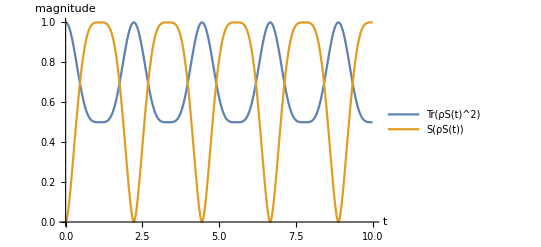

```mathematica
(* Assume at t=0 qubit 1 is in 0 state, qubit 2 is in 1 state *)
(* Construct the corresponding density matrix rho_SE(t=0): *)
ρSE0 = KP[P0,P1]; (* P0 and P1 are single qubit projection operators inot the states |0> and |1> *)
Print["ρSE0 = ",ρSE0 //MatrixForm]
(* Here is the simplified 2-qubit Jaynes-Cummings Hamiltonian, with two coupling constants c1, c2: *)
HJC = -c1 KP[PauliMatrix[3],Id[2]]-c2(KP[sp,sm]+KP[sm,sp]) ;
(* Construct the unitary time evolution operator out of this Hamiltonian: *)
Ut = MatrixExp[-I*HJC*t];
(* and the inverse: *)
Utd= MatrixExp[I*HJC*t];
(* Now time evolve the density matrix rho_SE(t): *)
ρSEt =FullSimplify[ Ut.ρSE0 .Utd];
(* Take the partial trace of the time-evolved density matrix over the "environmental" qubit: *)
ρSt = {{ρSEt[[1,1]]+ρSEt[[2,2]],ρSEt[[1,3]]+ρSEt[[2,4]]},{ρSEt[[3,1]]+ρSEt[[4,2]],ρSEt[[3,3]]+ρSEt[[4,4]]}};
(* Let's evaluate the partially traced density matrix rho_S(t) for simple values of the coupling constants: *)
c1=1;c2=1;
(* Force Mathematica to write rho_S(t) nicely: *)
Simplify[ρSt /.{Cos[2 √2 t]->2Cos[√2 t]^2-1},Trig->False]//MatrixForm

 (* Plot the trace of the square of rho_S(t), and the entanglement entropy S(rho_S(t)),
as a function of time: *)
Plot[{Chop[Tr[ρSt.ρSt]],SE[ρSt]},{t,0,10},AxesLabel->{"t","magnitude"},LabelStyle->Directive[Bold,FontFamily->"Helvetica",14],BaseStyle->AbsoluteThickness[2],PlotLegends->{"Tr(ρS(t)^2)","S(ρS(t))"}]
Clear[c1,c2];
```

## Quantum Decoherence Experiment #2: 2-qubit Environment We assume that qubit 1 is a 2-level atom and is our “system” qubit, while qubits 2 and 3 are “environment” qubits. We assume that the interaction of the system with the environment is via a simple Hamiltonian inspired by the Jaynes-Cummings Hamiltonian

ρSE0 = (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(a1+b2+c3+d4 | a5+b6+c7+d8
e1+f2+g3+h4 | e5+f6+g7+h8)

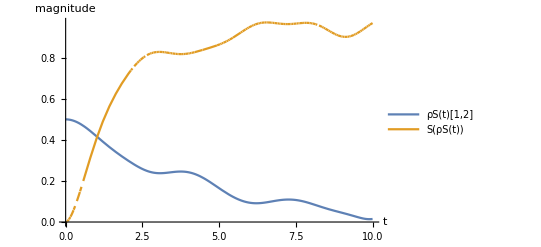

```mathematica
(* Assume at t=0 qubit 1 is in the + state *)
(* Construct the density matrix for this: *)
ρh = (1/2)*{{1,1},{1,1}};
(* Assume that at t=0 qubit 2 is in 0 state, qubit 3 is in the 1 state *)
(* Construct the full 3-qubit density matrix at t=0 as an 8x8 matrix *)
ρSE0 = KP[ρh,KP[P0,P1]];
Print["ρSE0 = ",ρSE0 //MatrixForm]
(* Here is the simplified Hamiltonian that couples the system qubit
to the environment qubits, with five coupling constants c11, c22, c33, c12, c13: *)
HJC =  -c11*KP[PauliMatrix[3],Id[4]]-c22*KP[Id[2],KP[PauliMatrix[3],Id[2]]] -c33*KP[Id[2],KP[Id[2],PauliMatrix[3]]]-c12*(KP[sp,KP[sm,Id[2]]]+KP[sm,KP[sp,Id[2]]]) -c13*(KP[sp,KP[Id[2],sm]]+KP[sm,KP[Id[2],sp]]) ;
(* Construct the unitary time evolution operator out of this Hamiltonian: *)
Ut = MatrixExp[-I*HJC*t];
(* and the inverse: *)
Utd= MatrixExp[I*HJC*t];
(* Choose some simple values for the couplings: *)
c11=0.9;
c22=0.3;
c33=0.4;
c12=0.5;
c13=0.4;
(* Now time evolve the density matrix rho_SE(t): *)
ρSEt =FullSimplify[ Ut.ρSE0 .Utd];
(* Take the partial trace of the time-evolved density matrix rho_SE(t) over the 2 environmental qubits: *)
(* First use the TraceSystem routing to see what this looks like for a general 8x8 matrix: *)
TraceSystem[({{a1, a2, a3, a4, a5, a6, a7, a8}, {b1, b2, b3, b4, b5, b6, b7, b8}, {c1, c2, c3, c4, c5, c6, c7, c8}, {d1, d2, d3, d4, d5, d6, d7, d8}, {e1, e2, e3, e4, e5, e6, e7, e8}, {f1, f2, f3, f4, f5, f6, f7, f8}, {g1, g2, g3, g4, g5, g6, g7, g8}, {h1, h2, h3, h4, h5, h6, h7, h8}}),{2,3}] //MatrixForm
(* Now do it for rho_SE(t) to get rho_S(t): *)
ρSt = TraceSystem[ρSEt,{2,3}];

 (* Plot the trace of the square of rho_S(t), and the entanglement entropy S(rho_S(t)),
as a function of time: *)
interf[tt_]:=Chop[Abs[ρSt[[1,2]]/.t->tt*1.0]]
Plot[{interf[t],SE[ρSt]},{t,0,10},AxesLabel->{"t","magnitude"},LabelStyle->Directive[Bold,FontFamily->"Helvetica",14],BaseStyle->AbsoluteThickness[2],PlotLegends->{"ρS(t)[1,2]","S(ρS(t))"}]
Clear[c11,c22,c33,c12,c13];
```

## Quantum Decoherence Experiment #3: Kraus operators We assume that qubit 1 is our “system” qubit while qubit 2 is our “environment” qubit. We assume that the interaction of the system with the environment is via a simple Hamiltonian inspired by the Jaynes-Cummings Hamiltonian

```mathematica
Clear[c1,c2,c3];
(* At t=0 qubit 1 is in + state, qubit 2 is in 0 state *)
(* Assume at t=0 qubit 1 is in the + state *)
(* Construct the density matrix for this: *)
ρh = (1/2)*{{1,1},{1,1}};
(* Assume that at t=0 qubit 2 is in 0 state *)
(* Construct the full 2-qubit density matrix at t=0 as a 4x4 matrix *)
ρSE0 = KP[ρh,P0];
Print["ρSE0 = ",ρSE0 //MatrixForm]
(* Here is the simplified Hamiltonian that couples the system qubit
to the environment qubit, with coupling constants c1, c2, c3: *)
HJC = -c1*(KP[sp,sm]+KP[sm,sp]) -c2*KP[PauliMatrix[3],Id[2]]-c3*KP[Id[2],PauliMatrix[3]];
(* Construct the unitary time evolution operator out of this Hamiltonian: *)
Ut = MatrixExp[-I*HJC*t];
(* and the inverse: *)
Utd= MatrixExp[I*HJC*t];
(* Choose some simple values for the couplings: *)
c1=1.0;
c2=1.0;
c3=1.0;
(* Construct the 2x2 Kraus operators out of the elements 
of the 4x4 unitary time evolution operator;
the 2x2 Kraus operators act in the system space;
they are neither unitary nor Hermitian *)
E11={{Ut[[1,1]],Ut[[1,3]]},{Ut[[3,1]],Ut[[3,3]]}};
E22={{Ut[[2,2]],Ut[[2,4]]},{Ut[[4,2]],Ut[[4,4]]}};
E12={{Ut[[1,2]],Ut[[1,4]]},{Ut[[3,2]],Ut[[3,4]]}};
E21={{Ut[[2,1]],Ut[[2,3]]},{Ut[[4,1]],Ut[[4,3]]}};
E11d=ConjugateTranspose[E11];
E22d=ConjugateTranspose[E22];
E12d=ConjugateTranspose[E12];
E21d=ConjugateTranspose[E21];
(* Now time evolve the density matrix rho_SE(t): *)
ρSEt =FullSimplify[ Ut.ρSE0 .Utd];
(* Take the partial trace over the environmental qubit to get rho_S(t): *)
ρSt = {{ρSEt[[1,1]]+ρSEt[[2,2]],ρSEt[[1,3]]+ρSEt[[2,4]]},{ρSEt[[3,1]]+ρSEt[[4,2]],ρSEt[[3,3]]+ρSEt[[4,4]]}};
(* Here is the Kraus operator verion of the same thing, 
valid if the initial state of the environmental qubit is 0 *)
ρStp0=E11.ρh .E11d+E21.ρh .E21d;
(* Here is the Kraus operator verion of the same thing, 
valid if the initial state of the environmental qubit has been 1 *)
ρStp1=E12.ρh .E12d+E22.ρh .E22d; 
(* Check that the Kraus version is correct by comparing at t=1: *)
Print["rho_S(t=1) = ",Chop[ρSt /.{t->1}]//MatrixForm];
Print["(Kraus version) = ",Chop[ρStp0 /.{t->1}]//MatrixForm];
(* Show the Kraus operators at t=1, to see that they are neither unitary nor Hermitian: *)
Print["E11(t=1) = ",Chop[E11/.{t->1}]//MatrixForm];
Print["E12(t=1) = ",Chop[E12/.{t->1}]//MatrixForm];
Print["E21(t=1) = ",Chop[E21/.{t->1}]//MatrixForm];
Print["E22(t=1) = ",Chop[E22/.{t->1}]//MatrixForm];
(* Try to construct 2x2 single qubit projection operators 
out of the Kraus operators; they approximately obey the usual
relations of projection operators: *)
Print["P11 + P12 = ",Chop[(E11.E11d+E12.E12d)/.{t->1}]//MatrixForm];
Print["P21 + P22 = ",Chop[(E21.E21d+E22.E22d)/.{t->1}]//MatrixForm];
Print["P11.P12 = ",Chop[(E11.E11d.E12.E12d)/.{t->1}]//MatrixForm];
Print["P21.P22 = ",Chop[(E21.E21d.E22.E22d)/.{t->1}]//MatrixForm];
Print["P11 = ",Chop[(E11.E11d)/.{t->1}]//MatrixForm];
Print["P11.P11 = ",Chop[(E11.E11d.E11.E11d)/.{t->1}]//MatrixForm];
Print["P12 = ",Chop[(E12.E12d)/.{t->1}]//MatrixForm];
Print["P12.P12 = ",Chop[(E12.E12d.E12.E12d)/.{t->1}]//MatrixForm];
Print["P21 = ",Chop[(E21.E21d)/.{t->1}]//MatrixForm];
Print["P21.P21 = ",Chop[(E21.E21d.E21.E21d)/.{t->1}]//MatrixForm];
Print["P22 = ",Chop[(E22.E22d)/.{t->1}]//MatrixForm];
Print["P22.P22 = ",Chop[(E22.E22d.E22.E22d)/.{t->1}]//MatrixForm];
```

ρSE0 = (1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0
1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0)

rho_S(t=1) = (0.854037 | -0.112423+0.245648 ⅈ
-0.112423-0.245648 ⅈ | 0.145963)

(Kraus version) = (0.854037 | -0.112423+0.245648 ⅈ
-0.112423-0.245648 ⅈ | 0.145963)

E11(t=1) = (-0.416147+0.909297 ⅈ | 0
0 | 0.540302)

E12(t=1) = (0 | 0
0.+0.841471 ⅈ | 0)

E21(t=1) = (0 | 0.+0.841471 ⅈ
0 | 0)

E22(t=1) = (0.540302 | 0
0 | -0.416147-0.909297 ⅈ)

P11 + P12 = (1. | 0
0 | 1.)

P21 + P22 = (1. | 0
0 | 1.)

P11.P12 = (0 | 0
0 | 0.206705)

P21.P22 = (0.206705 | 0
0 | 0)

P11 = (1. | 0
0 | 0.291927)

P11.P11 = (1. | 0
0 | 0.0852211)

P12 = (0 | 0
0 | 0.708073)

P12.P12 = (0 | 0
0 | 0.501368)

P21 = (0.708073 | 0
0 | 0)

P21.P21 = (0.501368 | 0
0 | 0)

P22 = (0.291927 | 0
0 | 1.)

P22.P22 = (0.0852211 | 0
0 | 1.)

## Notes end here for now